# Stylized facts in financial time series

Stylized facts are statistical properties emerging from the returns of financial time series that are present in almost every market.

## Getting stylized facts from an index

Although the mechanism which generates the financial time series it is not fully understood, making impossible to have a prediction on the next stock price, there are however some statistical properties inherent to the financial time series, these are called stylized facts. We can explore them using the FinancialData function, that conveniently can load the stock prices and returns.

Stylized facts are the result of many independent empirical studies on the statistical properties of financial markets that have been proven to be common across financial markets.

This is how a financial time series usually look like: Random, noisy and in some cases similar to a random walk. In this case since we are using an index that tracks the most successful companies in an stock market it has a tendency of growth.

We will start this exploration using the Mexican index IPC because it has had a growth in efficiency that can be seen in the stylized facts.

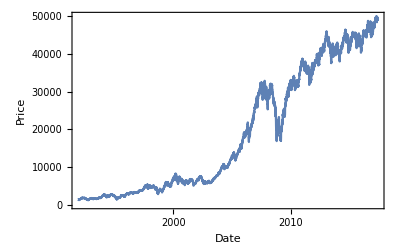

```mathematica
DateListPlot[FinancialData["^MXX",All],PlotRange->Full,FrameLabel->{"Date","Price"}]
```

To get the stylized facts we need to compute the returns, that are a stationary measure of the price changes. Returns are defined as the price difference in a timespan.

```mathematica
returns = FinancialData["^MXX","Return",All];
```

Let us plot the returns

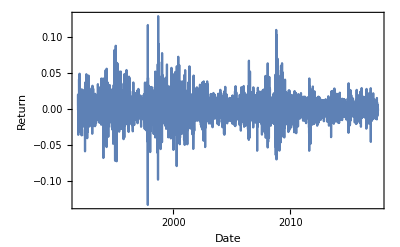

```mathematica
DateListPlot[returns,PlotRange->Full,Frame->True,FrameLabel->{"Date","Return"}]
```

The first stylized fact is that returns lack autocorrelations. This is actually to be expected in an efficient market, because present prices have to reflect all information that is currently know of the market (assuming that investors are rational), making impossible to make a future prediction because the expected value of the future price would have to be the present price.

Since FinancialData by default return the data in the {Date, Value} format, which was used to make the plots, we will have to separate each one into two variables in order to make the analysis.

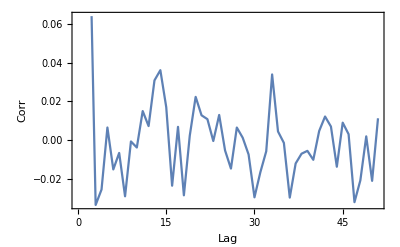

```mathematica
dates = returns[[All,1]]; values = returns[[All,2]];
ListLinePlot[CorrelationFunction[values,{50}],Frame->True,FrameLabel->{"Lag","Corr"}]
```

But investors are not always rational, so autocorrelation in fact can be used to as an indicator of the efficiency of the market. More efficient markets often are less autocorrelated.

We can plot the same data in different time windows and look at the value of autocorrelation at lag = 2. As time passes this market becomes more efficient.

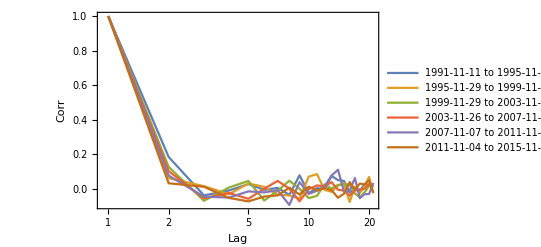

```mathematica
ListPlot[Map[CorrelationFunction[#,{20}]&,Partition[values,1000]],Joined->True,ScalingFunctions->{"Log",None},PlotRange->Full,PlotLegends->Map[DateString[First[#],"ISODate"]<>" to "DateString[Last[#],"ISODate"]&,Partition[dates,1000]],Frame->True,FrameLabel->{"Lag","Corr"}]
```

The autocorrelation of the absolute returns decays slowly

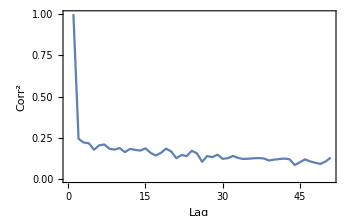

```mathematica
ListLinePlot[CorrelationFunction[Abs[returns[[All,2]]],{50}],PlotRange->Full,Frame->True,FrameLabel->{"Lag","Corr^2"}]
```

This slow decay is explained by the volatility clustering. Volatility clustering means that the price change is mostly followed by another with similar magnitude.
There is an aggregational gaussianity on the returns, when calculated with time intervals Δt.

```mathematica
Drop
```

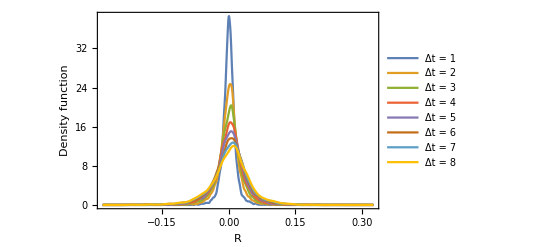

```mathematica
prices = FinancialData["^MXX",All];
Returns[x_,Δt_]:= N[Log[Take[x[[All,2]],{1+Δt,-1}]]-Log[Take[x[[All,2]],{1,-(1+Δt)}]]];
SmoothHistogram[Table[Returns[prices,Δt],{Δt,1,8}],PlotRange->Full,PlotLegends->Table["Δt = " <> ToString[i],{i,1,8}],Frame->True,FrameLabel->{"R","Density function"}]
```

This convergence to a gaussian distribution as Δt increases, is apparent in the evolution of the kurtosis that converges to the normal distribution kurtosis value.

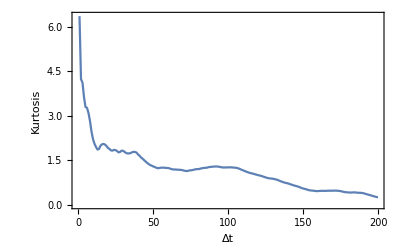

```mathematica
ListLinePlot[Table[Kurtosis[Returns[prices,Δt]],{Δt,1,200}] - Kurtosis[NormalDistribution[]],Frame->True,FrameLabel->{"Δt","Kurtosis"},PlotRange->Full]
```

Most measures of volatility of an asset are negatively correlated with the returns of that asset. This is the leverage effect. This happens because high volatility usually means a market in panic, where prices go down. Let us define the volatility as the absolute value of the returns and visualize it.

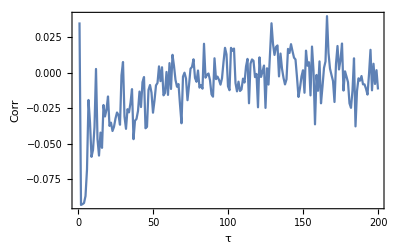

```mathematica
s = Returns[prices,1];
ListLinePlot[Table[{τ,Correlation[Abs[s[[τ;;-1]]],s[[1;;-τ]]]},{τ,1,200}],Frame->True,FrameLabel->{"τ","Corr"}]
```

Returns’ distributions are characterized by heavy tails. A simple way to view this fact is to plot the histogram in a logarithmic vertical scale. Since the distribution is a power law, the histogram has a linear profile. In some cases there could be some events with abnormally large values that do not follow a power law. These are often indicators of an economic crisis.

Notice that we are taking the positive values of the returns. One can also do exactly the same analysis for the negative part of the distribution.

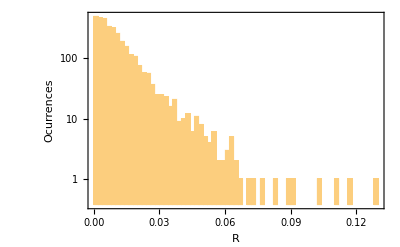

```mathematica
positiveValues = Select[returns,Last[#]≥0&];
Histogram[positiveValues[[All,2]],ScalingFunctions->{None,"Log"},PlotRange->All,Frame->True,FrameLabel->{"R","Ocurrences"}]
```

To find the point γ_left where the power law tails begin and the point γ_right where the extreme event begins we can use the Anderson-Darling statistic. This code computes the Anderson-Darling statistic in a range of γ test points and selects the most plausible one.

```mathematica
AndersonDarling[data_,γ_]:= Module[{s, n,α,z,A2},
s = Sort[data];
n = Count[data,x_/;x≥γ];
If[n>1,
s = Drop[s,Length[s]-n];
α = (Total[Log[s/γ]]/n)^-1;
z = Table[1-(γ/s[[i]])^α,{i,1,n}];
A2 = -n-(1/n)*Total[(2 Range[n]-1)*(Log[z]+Log[1-Reverse[z]])]; 
Return[A2];,
Return[∞];
];
];
LeftCutoff[data_,γmin_,γmax_,dγ_]:=Module[{tbl,minPos},
tbl = Table[{γ,AndersonDarling[data,γ]},{γ,γmin,γmax,dγ}];
tbl = DeleteCases[tbl,{_,∞}];
Extract[tbl[[All,1]], Ordering[tbl[[All,2]],1]]
];
RightCutoff[data_,γmin_,γmax_,dγ_]:=Module[{tbl,maxPos,left},
left = LeftCutoff[data,γmin,γmax,dγ];
tbl = Table[{γ,AndersonDarling[data,γ]},{γ,γmax,left,-dγ}];
tbl = DeleteCases[tbl,{_,∞}];
Extract[tbl[[All,1]], Ordering[tbl[[All,2]],-1]]
];
```

We can then select the point γ_left from where the power law tail begin.

```mathematica
γleft = LeftCutoff[positiveValues[[All,2]],0.01,0.08,0.0001]
```

0.0455

And the point γ_right from where the extreme events begin.

```mathematica
γright = RightCutoff[positiveValues[[All,2]],0.01,0.08,0.0001]
```

0.0633

Then we can visualize the points by adding them to the histogram.

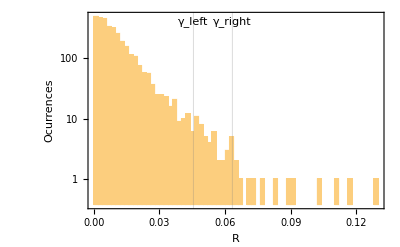

```mathematica
Histogram[positiveValues[[All,2]],ScalingFunctions->{None,"Log"},PlotRange->All,GridLines->{{γleft,γright},None},Frame->True,FrameLabel->{"R","Ocurrences"},Epilog->{Inset[Text["γ_left"],{γleft,6}],Inset[Text["γ_right"],{γright,6}]}]
```

To make sure we found the rightγ_left point we can just ask Mathematica to find the distribution of the points right from it and check if it returns a Pareto like distribution.

```mathematica
FindDistribution[Select[returns[[All,2]], #>γleft&]]
```

ParetoDistribution[7.,49.4139,1.64916,0.0455895]

Now we have a list of extreme events with their dates.

```mathematica
extremeEvents = Select[positiveValues,Last[#]>γright&];
Grid[{{"Date","Price change"}}~Join~extremeEvents,Frame->All]
```

Date | Price change
{1994,12,22} | 0.0821327
{1995,1,31} | 0.0880388
{1995,3,10} | 0.0642549
{1995,3,24} | 0.06331
{1997,10,28} | 0.116888
{1998,9,15} | 0.12923
{1998,9,23} | 0.0908015
{1998,10,15} | 0.0655278
{1999,1,15} | 0.0778111
{2000,6,2} | 0.0727218
{2006,6,15} | 0.0672672
{2008,1,22} | 0.0635898
{2008,10,13} | 0.110052
{2008,10,28} | 0.103102
{2008,11,24} | 0.0700132
{2009,4,13} | 0.0637258

We can plot the dates that correspond to the extreme events.

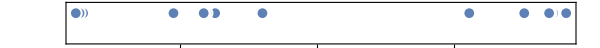

```mathematica
TimelinePlot[extremeEvents[[All,1]]]
```

Notice that most of them are packed together around known market crashes, so we can use FindClusters to find which extreme events correspond to a known market crash.

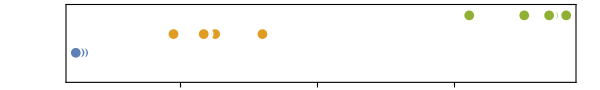

```mathematica
TimelinePlot[FindClusters[Map[DateObject,extremeEvents[[All,1]]]]]
```

Distributions are often asymmetrical around the origin, this is considered an stylized fact. One way to test if a sample comes from a symmetric distribution is to use the T_n statistic which can be implemented with the following code.

```mathematica
Tn[Y_]:= Module[{n,X,loglik,kx,fnleft,fnminus},
n = Length[Y];
X = Sort[Y];
loglik =Sum[
kx = Abs[X[[i]]];
fnleft = Count[X, x_/;x<kx];
fnminus = Count[X, x_/;x≤ -kx];
Piecewise[{{fnminus*Log[(fnminus+n-fnleft)/(2 fnminus)],fnminus>0},{0,fnminus ≤ 0}}]+Piecewise[{{(n-fnleft)*Log[(fnminus+n-fnleft)/(2(n-fnleft))],fnleft < n},{0,fnleft ≥ n}}]
,{i,1,n}
];
Return[N[-2loglik/n]];
];
Tn[Y_,c_]:=Tn[Y-c];
```

Then to test the symmetry around 0 we evaluate the T_n statistic with c=0 and check if it’s value is under the confidence interval. If it is not we have to reject the null hypothesis that the data came from a symmetric distribution. The upper percentage points values are 4.909, 2.983 and 2.2 respectively and were taken from the literature.

Since the Mexican market it’s not as efficient as US markets we will showcase this behavior using the S&P 500 index. Also because this method it’s computationally expensive we will use a sub sample of 1000 values of the returns.

```mathematica
returns = FinancialData["^GSPC","Return",All];
smallreturnssample = Take[returns[[All,2]],1000];
If[Tn[smallreturnssample,0] < 2.983,"Symmetric","Assymetric"]
```

Assymetric

If we are interested in checking where is the most plausible point of symmetry we can compute the T_n statistic in multiple symmetry test points c.

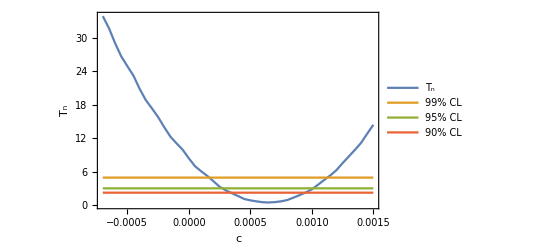

```mathematica
cmin = -0.0007;
cmax = 0.0015;
Δc = 0.00005;
sim = Table[{c,Tn[smallreturnssample,c]},{c,cmin,cmax,Δc}];
upp1 = {{cmin, 4.909},{cmax,4.909}};
upp2 = {{cmin, 2.983},{cmax,2.983}};
upp3 = {{cmin, 2.2},{cmax,2.2}};
ListPlot[{sim,upp1,upp2,upp3},Joined->True,Frame->True,FrameLabel->{"c","T_n"},PlotLegends->{"T_n","99% CL","95% CL","90% CL"}]
```

So the most plausible point of symmetry of the returns is

```mathematica
MinimalBy[sim,Last][[1,1]]
```

0.00065

## A simple system with stylized facts: the game of life

One of the reasons of the relevance of stylized facts is that they allow us to construct models of financial markets under a microscopic point of view, and assess their effectiveness by checking if they are still able to reproduce the stylized facts. Many artificial stock markets have been modelled as agent based models or cellular automata models, and in fact even the game of life exhibits stylized facts. We will now search for them.

We will iterate 2000 times the game of life with a board of 200x200. The greater the board the better the results will be.

```mathematica
n =200;
gol = CellularAutomaton["GameOfLife",RandomInteger[1,{n,n}],2000];
ListAnimate[Map[ArrayPlot,Take[gol,300]]]
```

Let’s define the “center of mass” of the game of life as

```mathematica
RCM[gol_]:=1/n Sum[gol[[i,j]]({i,j}-n/2),{i,1,n},{j,1,n}];
```

Then we can get all the center of masses. It looks like a random walk.

```mathematica
rcms = Map[RCM,gol];
Animate[ListLinePlot[rcms,AspectRatio->1,Frame->True,FrameLabel->{"x","y"},Epilog->{PointSize[Large],Point[rcms[[i]]]}],{i,1,Length[rcms],1},AnimationRate->10,SaveDefinitions->True]
```

Then to construct a time series we can take the norm of the center of masses, and obtain a time series r. This r will be the observable of the system.

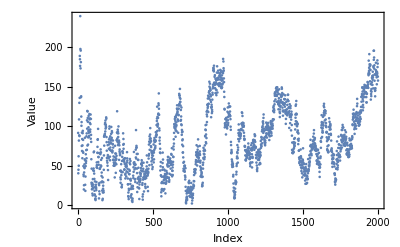

```mathematica
r = N[Map[Norm,rcms]];
ListPlot[r,Frame->True,FrameLabel->{"Index","Value"}]
```

Returns show a more complicated structure that indicates that this is not a simple random walk. One can check by plain sight that there is some degree of volatility clustering.

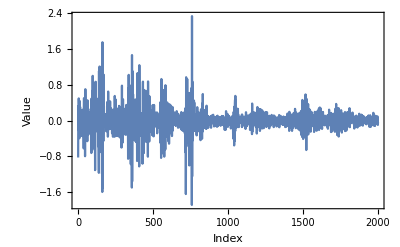

```mathematica
Returns[x_,Δt_]:= N[Log[Drop[x,Δt]]-Log[Take[x,{1,-(1+Δt)}]]];
ListLinePlot[Returns[r,1],Frame->True,FrameLabel->{"Index","Value"},PlotRange->Full]
```

There is aggregational gaussianity

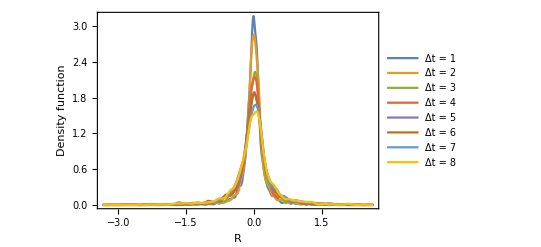

```mathematica
SmoothHistogram[Table[Returns[r,Δt],{Δt,1,8}],PlotRange->Full,PlotLegends->Table["Δt = " <> ToString[i],{i,1,8}],Frame->True,FrameLabel->{"R","Density function"}]
```

as is evidenced by the convergence of the kurtosis.

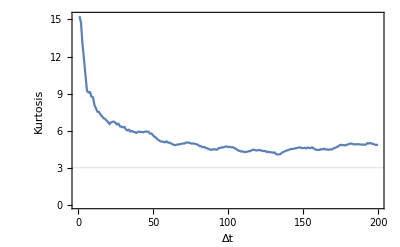

```mathematica
ListLinePlot[Table[Kurtosis[Returns[r,Δt]],{Δt,1,200}],Frame->True,FrameLabel->{"Δt","Kurtosis"},PlotRange->Full,GridLines->{None,{3}}]
```

The fat tails are a bit more tricky to visualize.

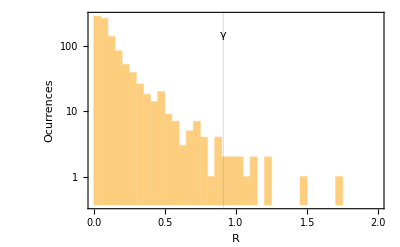

```mathematica
posValues = Select[Returns[r,1],#≥0&];
γ = LeftCutoff[posValues,0.1,1,0.01];
Histogram[posValues,ScalingFunctions->{None,"Log"},PlotRange->{{0,2},All},GridLines->{{γ},None},Epilog->{Inset[Text["γ"],{γ,5}]},Frame->True,FrameLabel->{"R","Ocurrences"}]
```

And it is not always clear to what degree they might be considered a power law.

```mathematica
FindDistribution[Select[Returns[r,1],#>γ&],3]
```

{WeibullDistribution[0.621736,0.248962,0.926959],ParetoDistribution[7.,3.41506,3.80454,0.926959],UniformDistribution[{0.926959,2.33015}]}

Slow decay of  absolute returns.

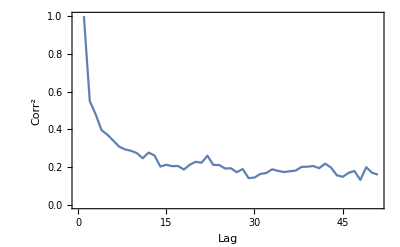

```mathematica
ListLinePlot[CorrelationFunction[Abs[Returns[r,1]],{50}],PlotRange->Full,Frame->True,FrameLabel->{"Lag","Corr^2"}]
```

And leverage effect.

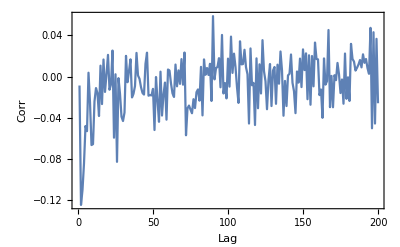

```mathematica
s = Returns[r,1];
ListLinePlot[Table[{τ,Correlation[Abs[s[[τ;;-1]]],s[[1;;-τ]]]},{τ,1,200}],Frame->True,FrameLabel->{"Lag","Corr"}]
```

It seems that financial markets share many properties with a simple game of life. One question that remains open is, do they share common properties? or are stylized facts very common properties found across a wide range of complex systems that arise when carefully selecting an observable?

Further Explorations

Investigate if the stylized facts still appear using other measures of returns

Implement a trading strategy based on the stylized facts

Authorship information

Carlos Manuel Rodríguez Martínez

2017/06/23

fis.carlosmanuel@gmail.com